```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
files = FileNames["*.csv", NotebookDirectory[]];
```

```mathematica
episodes = Select[files, StringContainsQ[#, "episode"]&];
predictions = Select[files, StringContainsQ[#, "prediction"]&];
```

```mathematica
obsV
```

Symbol[]

```mathematica
XPlots
```

{}

```mathematica
AppendTo[XPlots, Rasterize[Show[
ListLinePlot[Transpose[obsX]],
ListLinePlot[Transpose[predX], PlotStyle->Dashed],
PlotRange->All
]]]
```

{1,-Graphics-}

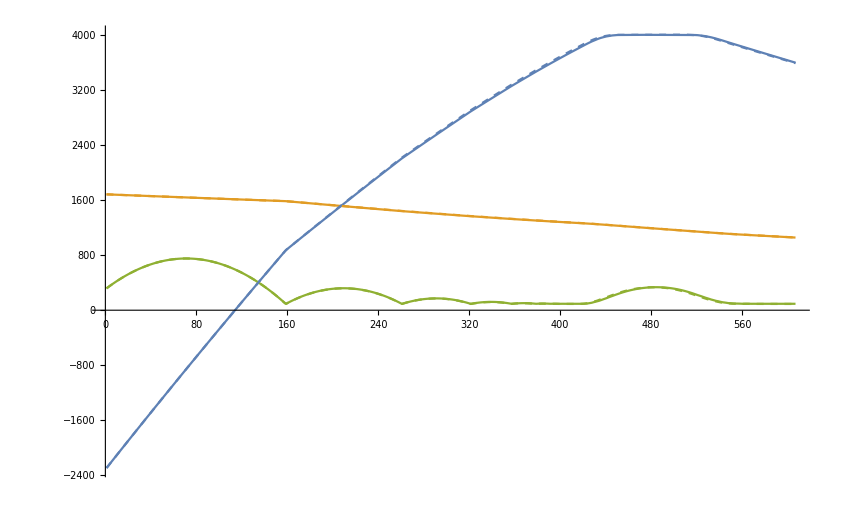

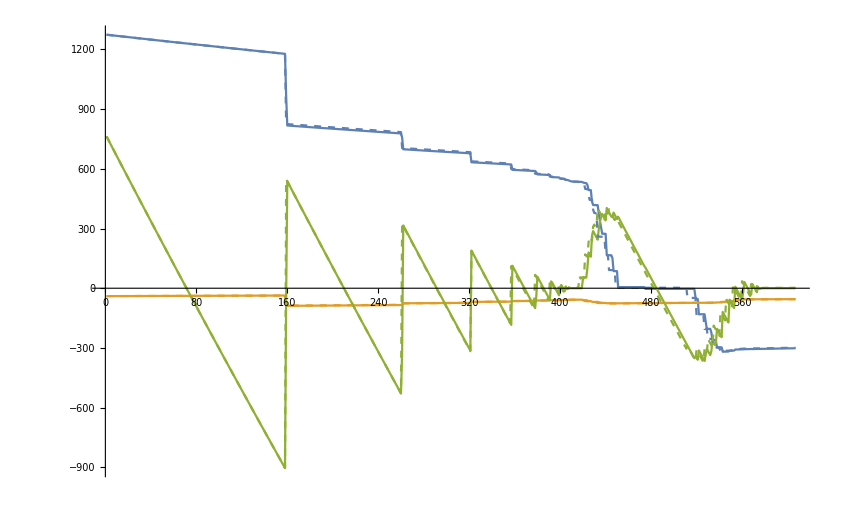

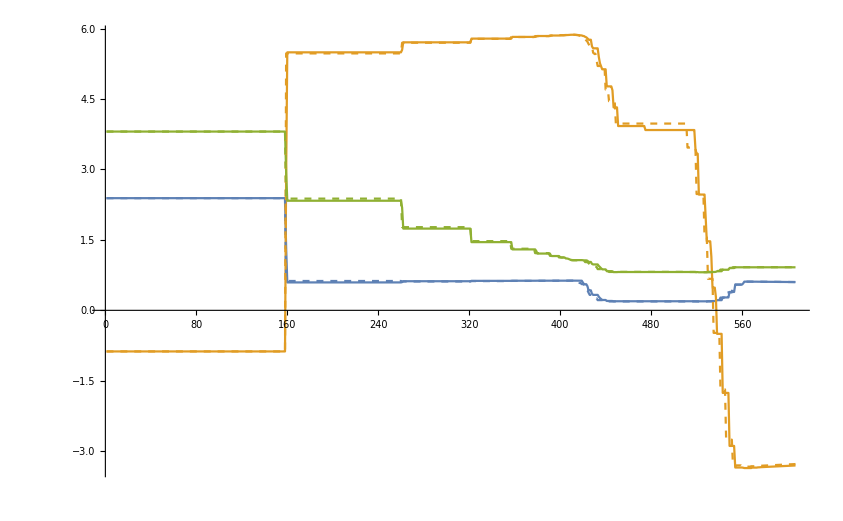

```mathematica
k = 122;
data = Import[episodes[[k]]];
obsX = data[[All, 2;;4]];
obsV = data[[All, 5;;7]];
obsW = data[[All, 11;;13]];
data = Import[predictions[[k]]];
predX = data[[All, 1;;3]];
predV = data[[All, 4;;6]];
predW = data[[All, 7;;9]];

Show[
ListLinePlot[Transpose[obsX]],
ListLinePlot[Transpose[predX], PlotStyle->Dashed],
PlotRange->All
]
Show[
ListLinePlot[Transpose[obsV]],
ListLinePlot[Transpose[predV], PlotStyle->Dashed],
PlotRange->All
]
Show[
ListLinePlot[Transpose[obsW]],
ListLinePlot[Transpose[predW], PlotStyle->Dashed],
PlotRange->All
]
```

```mathematica
field=-Graphics3D-;
```

```mathematica
edges = MeshPrimitives[field, 1];
```

```mathematica
Graphics3D[
edges,
Boxed->False,
ViewProjection->"Orthographic"
]
```

-Graphics3D-

```mathematica
Graphics3D[{
edges,
Opacity[1],
Red,
Line[obsX.({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}})],
Blue,
Line[predX.({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}})]
}, 
Boxed->True,
PlotRange->bounds,
ViewProjection->"Orthographic"]
```

-Graphics3D-

```mathematica
PlotRange
```

```mathematica
box[[1]]
```

{-5028.61,480.535,91.0377}

```mathematica
box = BoundingRegion[predX.({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}), "MinCuboid"]
inflate = 1000;
bounds = {
{box[[1,1]] - inflate, box[[2, 1]] + inflate},
{box[[1,2]] - inflate, box[[2, 2]] + inflate},
{box[[1,3]] - inflate, box[[2, 3]] + inflate}
};
```

Cuboid[{1056.8,-4004.65,90.9334},{1684.14,2294.52,751.732}]

```mathematica
bounds
```

{{-5028.61,-2943.25},{480.535,3049.32},{91.0377,1791.56}}